## The RGB Cube corners.

```mathematica
RGBCube = {{0,1,1,0,0,0,1,1},{0,0,1,1,1,0,0,1},{0,0,0,0,1,1,1,1}};
MatrixForm[RGBCube]
```

(0 | 1 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1)

```mathematica
RGBCube = {{0,1,0,0,0,1,1,1},{0,0,1,0,1,0,1,1},{0,0,0,1,1,1,0,1}};
MatrixForm[RGBCube]
```

(0 | 1 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1 | 1 | 0 | 1)

## Rotation Matrices

```mathematica
RotationMatrixX[α_]:={{1, 0, 0}, {0, Cos[α], Sin[α]}, {0, -Sin[α], Cos[α]}};
RotationMatrixY[β_]:={{Cos[β], 0, -Sin[β]}, {0, 1, 0}, {Sin[β], 0, Cos[β]}};
RotationMatrixZ[γ_]:={{Cos[γ], Sin[γ], 0}, {-Sin[γ], Cos[γ], 0}, {0, 0, 1}};
R[α_,β_, γ_]:=RotationMatrixZ[γ].RotationMatrixY[β].RotationMatrixX[α]
```

Solution for the Yab cube. Luminocity axis is in the X value.

```mathematica
YAB[θ_]:=RotationMatrixX[θ].RotationMatrixZ[ArcTan[1/Sqrt[2]]].RotationMatrixY[-Pi/4];
Print[MatrixForm[FullSimplify[YAB[θ]]].MatrixForm[RGBCube],"=",MatrixForm[FullSimplify[YAB[θ]. RGBCube]]]
```

(1/(√3) | 1/(√3) | 1/(√3)
-Cos[θ]/(√6)-Sin[θ]/(√2) | √(2/3) Cos[θ] | -Cos[θ]/(√6)+Sin[θ]/(√2)
-Cos[θ]/(√2)+Sin[θ]/(√6) | -√(2/3) Sin[θ] | Cos[θ]/(√2)+Sin[θ]/(√6)).(0 | 1 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1)=(0 | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | √3
0 | -Cos[θ]/(√6)-Sin[θ]/(√2) | Cos[θ]/(√6)-Sin[θ]/(√2) | √(2/3) Cos[θ] | Cos[θ]/(√6)+Sin[θ]/(√2) | -Cos[θ]/(√6)+Sin[θ]/(√2) | -√(2/3) Cos[θ] | 0
0 | -Cos[θ]/(√2)+Sin[θ]/(√6) | -Cos[θ]/(√2)-Sin[θ]/(√6) | -√(2/3) Sin[θ] | Cos[θ]/(√2)-Sin[θ]/(√6) | Cos[θ]/(√2)+Sin[θ]/(√6) | √(2/3) Sin[θ] | 0)

```mathematica
YABCube[θ_]:=FullSimplify[YAB[θ].RGBCube]
```

```mathematica
MatrixForm[YABCube[θ]]
```

(0 | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | √3
0 | -Cos[θ]/(√6)-Sin[θ]/(√2) | Cos[θ]/(√6)-Sin[θ]/(√2) | √(2/3) Cos[θ] | Cos[θ]/(√6)+Sin[θ]/(√2) | -Cos[θ]/(√6)+Sin[θ]/(√2) | -√(2/3) Cos[θ] | 0
0 | -Cos[θ]/(√2)+Sin[θ]/(√6) | -Cos[θ]/(√2)-Sin[θ]/(√6) | -√(2/3) Sin[θ] | Cos[θ]/(√2)-Sin[θ]/(√6) | Cos[θ]/(√2)+Sin[θ]/(√6) | √(2/3) Sin[θ] | 0)

```mathematica
MatrixForm[YABCube[0]]
```

(0 | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | √3
0 | -1/(√6) | 1/(√6) | √(2/3) | 1/(√6) | -1/(√6) | -√(2/3) | 0
0 | -1/(√2) | -1/(√2) | 0 | 1/(√2) | 1/(√2) | 0 | 0)

```mathematica
MatrixForm[YABCube[Pi/6]]
```

(0 | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | √3
0 | -1/(√2) | 0 | 1/(√2) | 1/(√2) | 0 | -1/(√2) | 0
0 | -1/(√6) | -√(2/3) | -1/(√6) | 1/(√6) | √(2/3) | 1/(√6) | 0)

```mathematica
MatrixForm[{TrigExpand[YABCube[θ +Pi/6][[2]]],YABCube[θ ][[3]]}]
```

(0 | -Cos[θ]/(√2)-Sin[θ]/(√6) | Cos[θ]/(√2)-Sin[θ]/(√6) | √(2/3) Sin[θ] | Cos[θ]/(√2)+Sin[θ]/(√6) | -Cos[θ]/(√2)+Sin[θ]/(√6) | -√(2/3) Sin[θ] | 0
0 | -Cos[θ]/(√2)+Sin[θ]/(√6) | -√(2/3) Sin[θ] | Cos[θ]/(√2)+Sin[θ]/(√6) | Cos[θ]/(√2)-Sin[θ]/(√6) | √(2/3) Sin[θ] | -Cos[θ]/(√2)-Sin[θ]/(√6) | 0)

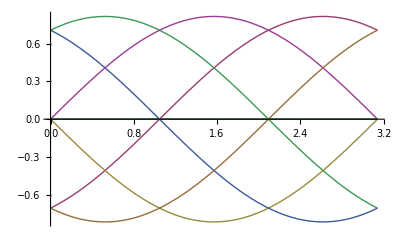

```mathematica
Plot[Evaluate[YABCube[θ][[3]], {θ, 0, Pi}]]
```

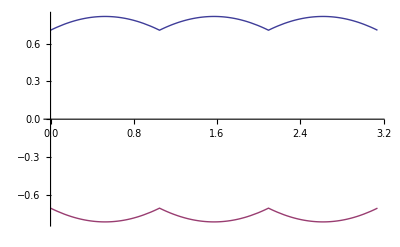

```mathematica
Plot[{Max[YABCube[θ ][[3]]],Min[YABCube[θ ][[3]]]},{θ,0,Pi}]
```

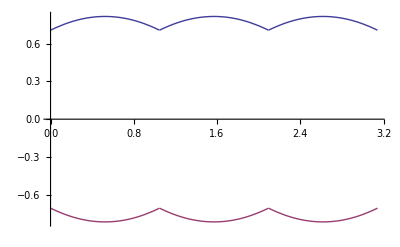

```mathematica
Plot[{Cos[Mod[θ,Pi/3]]/(√2)+Sin[Mod[θ,Pi/3]]/(√6),(-Cos[Mod[θ,Pi/3]])/(√2)-Sin[Mod[θ,Pi/3]]/(√6)},{θ,0,Pi}]
```

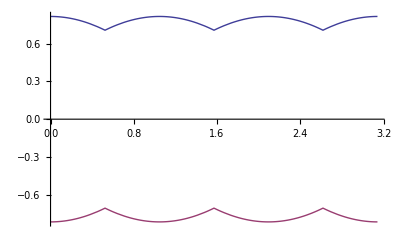

```mathematica
Plot[{Max[YABCube[θ ][[2]]],Min[YABCube[θ ][[2]]]},{θ,0,Pi}]
```

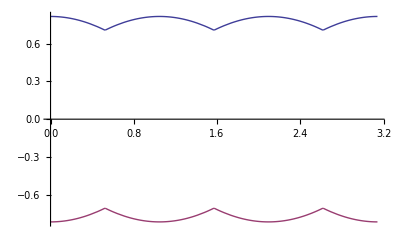

```mathematica
Plot[{Cos[Mod[θ -Pi/6,Pi/3]]/(√2)+Sin[Mod[θ-Pi/6,Pi/3]]/(√6),(-Cos[Mod[θ-Pi/6,Pi/3]])/(√2)-Sin[Mod[θ-Pi/6,Pi/3]]/(√6)},{θ,0,Pi}]
```

```mathematica
YABPolygon[θ_]:=Transpose[{Take[YABCube[θ ][[2]],{2,7}],Take[YABCube[θ ][[3]],{2,7}]}]
```

```mathematica
Manipulate[Graphics[{Red,Rectangle[Sequence@@Transpose[{YABAxisRanges[θ ][[2]],YABAxisRanges[θ ][[3]]}]],Blue,Polygon[YABPolygon[θ]]},PlotRange->{{-√(2/3) ,√(2/3) },{-√(2/3) ,√(2/3) }}],{θ,0,Pi}]
```

Part::partw: Part 2 of YABAxisRanges[0.333009] does not exist.

Part::partw: Part 3 of YABAxisRanges[0.333009] does not exist.

Transpose::nmtx: The first two levels of the one-dimensional list {YABAxisRanges[0.333009] ⟦ 2 ⟧, YABAxisRanges[0.333009] ⟦ 3 ⟧} cannot be transposed.

Part::partw: Part 2 of YABAxisRanges[0.333009] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
YABAxisRanges[θ_]:={{0,Sqrt[3]},{Cos[Mod[θ -Pi/6,Pi/3]]/(√2)+Sin[Mod[θ-Pi/6,Pi/3]]/(√6),(-Cos[Mod[θ-Pi/6,Pi/3]])/(√2)-Sin[Mod[θ-Pi/6,Pi/3]]/(√6)},{Cos[Mod[θ,Pi/3]]/(√2)+Sin[Mod[θ,Pi/3]]/(√6),(-Cos[Mod[θ,Pi/3]])/(√2)-Sin[Mod[θ,Pi/3]]/(√6)}}
```

```mathematica
scaleMatrix[θ_] := {{1/Sqrt[3],0,0},{0,Sqrt[3/2],0},{0,0,Sqrt[3/2]}};
YAB[θ_]:=scaleMatrix. RotationMatrixX[θ].RotationMatrixZ[ArcTan[1/Sqrt[2]]].RotationMatrixY[-Pi/4];
MatrixForm[FullSimplify[YAB[θ]]]
MatrixForm[FullSimplify[YAB[θ]. RGBCube]]
```

SetDelayed::write: Tag List in {{1/√3, 0, 0}, {0, √3/2, 0}, {0, 0, √3/2}}[θ_] is Protected.

(1/3 | 1/3 | 1/3
1/2 (-Cos[θ]-√3 Sin[θ]) | Cos[θ] | 1/2 (-Cos[θ]+√3 Sin[θ])
1/2 (-√3 Cos[θ]+Sin[θ]) | -Sin[θ] | 1/2 (√3 Cos[θ]+Sin[θ]))

(0 | 1/3 | 2/3 | 1/3 | 2/3 | 1/3 | 2/3 | 1
0 | 1/2 (-Cos[θ]-√3 Sin[θ]) | 1/2 (Cos[θ]-√3 Sin[θ]) | Cos[θ] | 1/2 (Cos[θ]+√3 Sin[θ]) | 1/2 (-Cos[θ]+√3 Sin[θ]) | -Cos[θ] | 0
0 | 1/2 (-√3 Cos[θ]+Sin[θ]) | 1/2 (-√3 Cos[θ]-Sin[θ]) | -Sin[θ] | 1/2 (√3 Cos[θ]-Sin[θ]) | 1/2 (√3 Cos[θ]+Sin[θ]) | Sin[θ] | 0)